```mathematica
pgg[r_,N_] := (N*r^2)^((N-1)/4)*BesselK[(1-N)/2,Sqrt[N*r^2]]/(2^((N-1)/2)*Gamma[N/2]*Sqrt[Pi/N])
```

```mathematica
NIntegrate[pgg[r,5],{r,-Infinity,+Infinity}]
```

NIntegrate::inumr: The integrand pgg[r, 5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

NIntegrate[pgg[r,5],{r,-∞,+∞}]

```mathematica
pga[r_,K_,L_,N_] :=(Gamma[L-(K+N)/2+1]Gamma[L-(K-1)/2]/(Gamma[L-(K+N-1)/2]*Gamma[N/2]*Sqrt[2*Pi*(2*L-K-N-1)/N]))*HypergeometricU[L-(K+N)/2+1,(1-N)/2+1,N*r^2/(2*(2*L-K-N-1))]
```

```mathematica
NIntegrate[pga[r,100,60,5],{r,-Infinity,+Infinity}]
```

1.

```mathematica
pag[r_,K_,l_,N_]:= Gamma[l-(K-N)/2]*Gamma[l-(K-1)/2]*HypergeometricU[l-(K-1)/2,1+(1-N)/2,N*r^2/(2*(2l-K-2))]/(Gamma[l-K/2]*Gamma[N/2]*Sqrt[2*Pi*(2l-K-2)/N])
```

```mathematica
NIntegrate[pag[r,100,60,5],{r,-Infinity,+Infinity}]
```

1.

```mathematica
paa[r_,K_,l_,L_,N_]:= Gamma[l-(K-1)/2]*Gamma[l-(K-N)/2]*Gamma[L-(K+N)/2+1]*Gamma[L-(K-1)/2]*Hypergeometric2F1[l-(K-1)/2,L-(K+N)/2+1,L+l-(K-1),1-N*r^2/((2*L-K-N-1)*(2*l-K-2))]/(Sqrt[Pi*(2*L-K-N-1)*(2*l-K-2)/N]*Gamma[l-K/2]*Gamma[L-(K+N-1)/2]*Gamma[L+l-(K-1)]*Gamma[N/2])
```

```mathematica
NIntegrate[paa[r,100,60,60,5],{r,-Infinity,+Infinity}]
```

1.

```mathematica
Plot[{pgg[r,5],pga[r,100,55,5],pag[r,100,55,5],paa[r,100,55,55,5]},{r,-2,+2}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.004], FrameLabel->{Style[OverTilde[r],35],Style[pdf,35]}, PlotStyle->Thickness[0.004]]
```

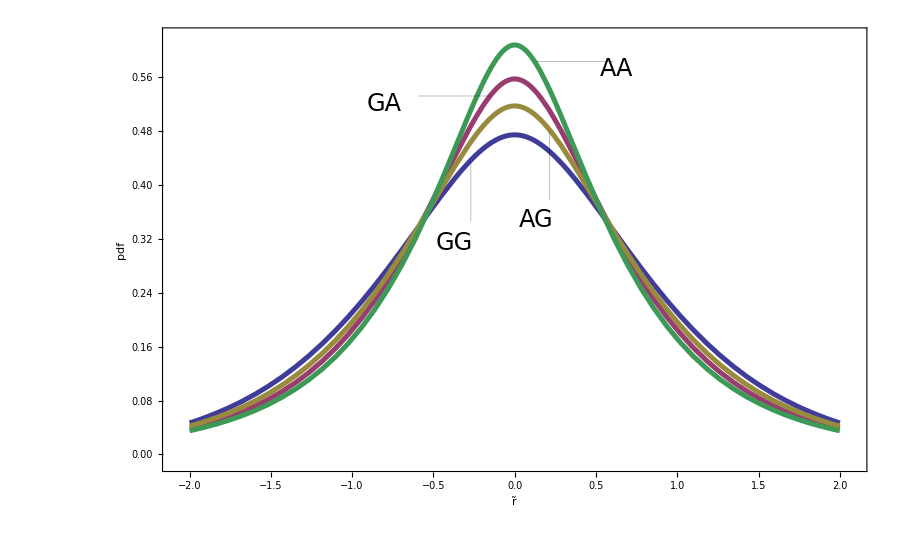

```mathematica
LogPlot[{pgg[r,5],pga[r,100,55,5],pag[r,100,55,5],paa[r,100,55,55,5]},{r,-8,+8}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.004], FrameLabel->{Style[OverTilde[r],35],Style[pdf,35]}, PlotStyle->Thickness[0.004]]
```

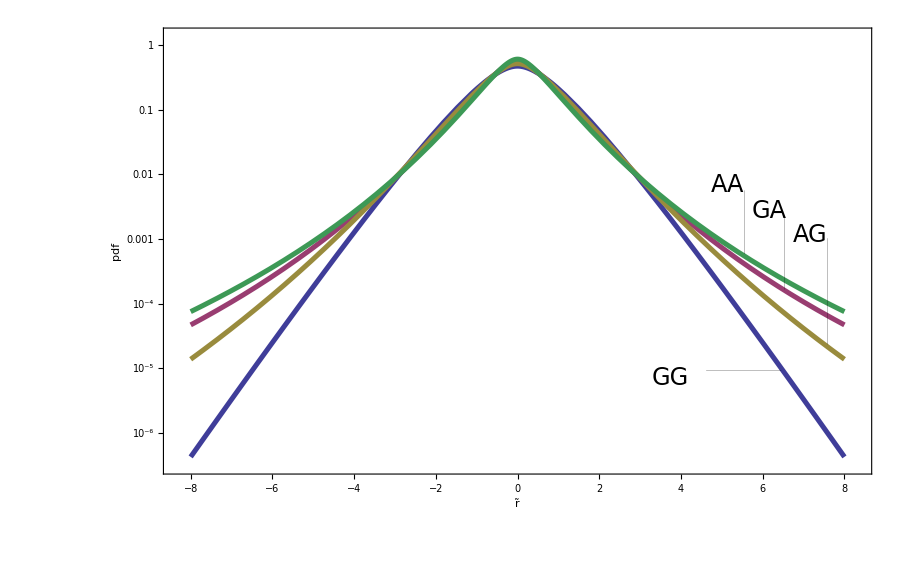

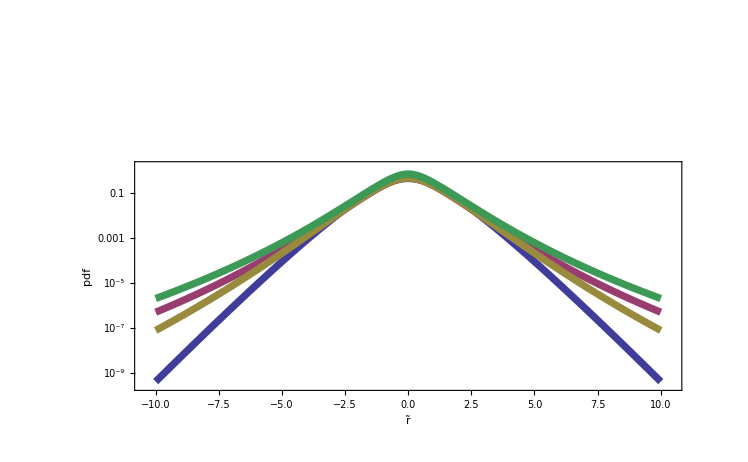

```mathematica
LogPlot[{pga[r,100,55,5],pga[r,100,60,5],pga[r,100,65,5],pga[r,100,70,5],pga[r,100,75,5]},{r,-8,+8}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.004], FrameLabel->{Style[OverTilde[r],35],Style[pdf,35]}, PlotStyle->Thickness[0.004]]
```

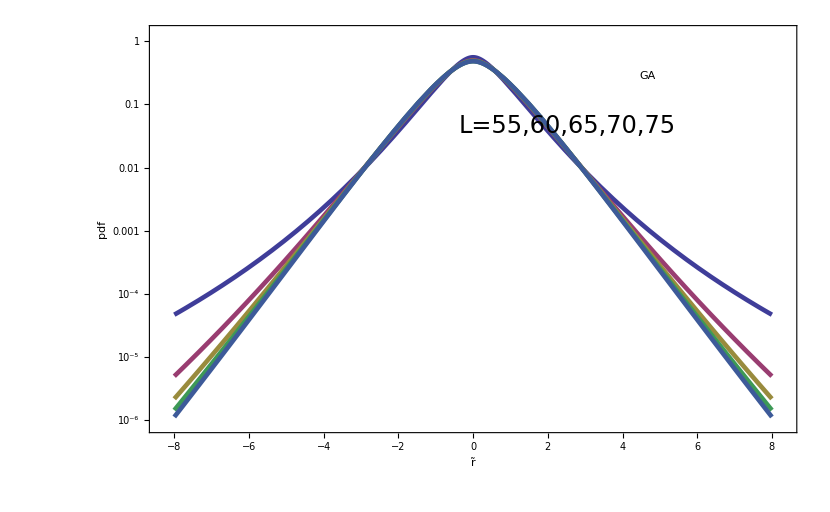

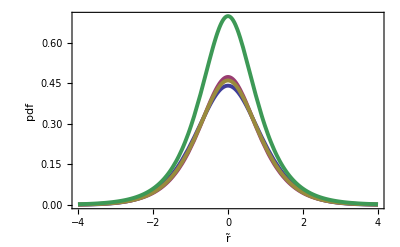

```mathematica
Plot[{pgg[r,8],pga[r,10,8],pag[r,10,8],paa[r,10,10,8]},{r,-4,+4}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.006], FrameLabel->{Style[OverTilde[r],20],Style[pdf,20]}, PlotStyle->Thickness[0.007]]
```

```mathematica
LogPlot[{pga[r,100,65,3],pga[r,100,65,6],pga[r,100,65,9],pga[r,100,65,12]},{r,-8,+8}, FrameTicksStyle-> Directive[20],Frame->True, FrameStyle->Thickness[0.004], FrameLabel->{Style[OverTilde[r],35],Style[pdf,35]}, PlotStyle->Thickness[0.004]]
```

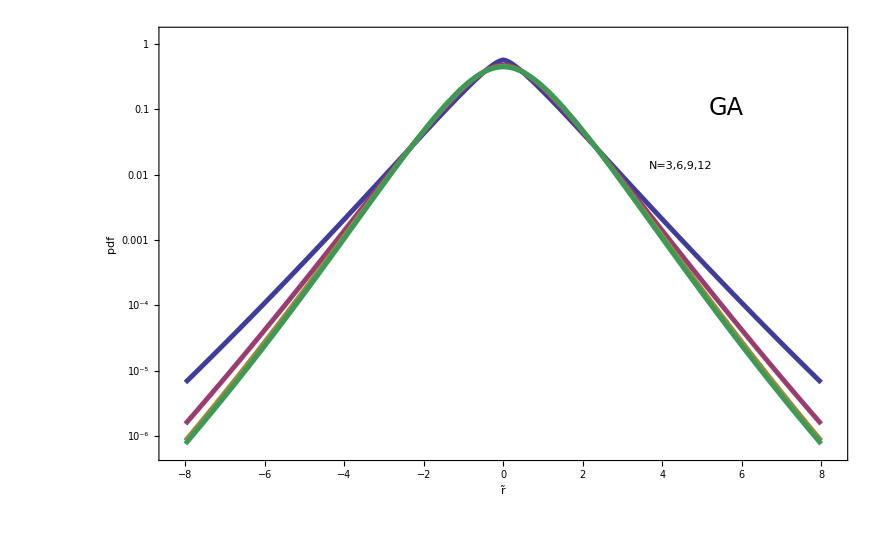

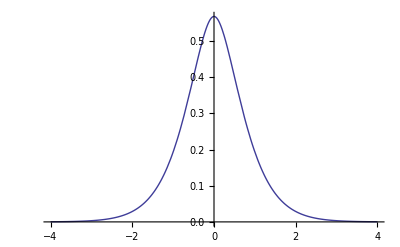

```mathematica
Plot[pga[r,300,500,5],{r,-4,+4}]
```

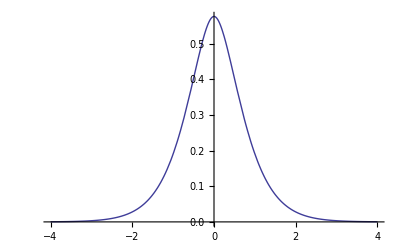

```mathematica
Plot[pga[r,30,50,5],{r,-4,+4}]
```

```mathematica
pag[r_,K_,l_,N_]:= Gamma[l+(N-1)/2]*Gamma[l]*HypergeometricU[l,1+(1-N)/2,N*r^2/(2*(2l-K-2))]/(Gamma[l-1/2]*Gamma[N/2]*Sqrt[2*Pi*(2l-K-2)/N])
```

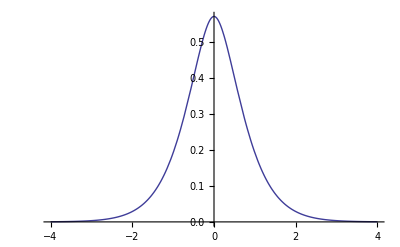

```mathematica
Plot[pag[r,30,50,5],{r,-4,+4}]
```

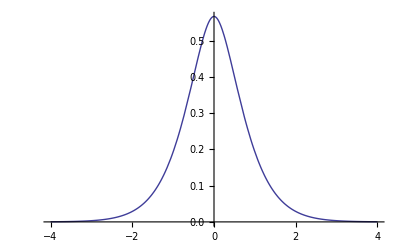

```mathematica
Plot[pag[r,300,500,5],{r,-4,+4}]
```